```mathematica
Clear["Global`*"]
```

```mathematica
f[k_]:=Module[{},
pt=Table[{{y^2/4,y},{y^2/4+(2*k)/Sqrt[4+y^2],y-(y*k)/Sqrt[4+y^2]}},{y,-9,9,0.1}];
Show[Graphics[{Orange,Thin,Line[#]}&/@pt,Axes->True,AspectRatio->Automatic],
ParametricPlot[{t^2/4,t},{t,-9,9},PlotStyle->Black],
ImageSize->Large]
]
```

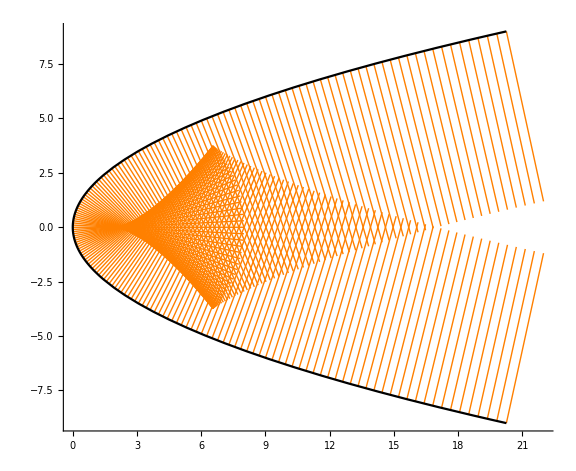

```mathematica
f[8]
```

```mathematica
c[t_]:=y-t+t/2*(x-t^2/4)
solxy={x,y}/.Solve[c[t]==0&&D[c[t],t]==0,{x,y}]//First
```

{1/4 (8+3 t^2),-t^3/4}

```mathematica
d=8;
solt=Solve[D[t^2/4+2*d/Sqrt[4+t^2],t]==0]
tmin=t/.solt[[2]]
```

{{t→0},{t→-2 √(-1+2 2^(1/3))},{t→2 √(-1+2 2^(1/3))}}

-2 √(-1+2 2^(1/3))

```mathematica
s1=Integrate[t^3/4*D[1/4*(8+3*t^2),t],{t,tmin,-tmin}]
s2=Integrate[(t-(t*d)/Sqrt[4+t^2])*D[t^2/4+2*d/Sqrt[4+t^2],t],{t,tmin,-tmin}]
s=s1+s2//N[#,16]&
```

24/5 (-1+2 2^(1/3))^(5/2)

-8/3 (√(735-1038 2^(1/3)+456 2^(2/3))+6 (ArcSinh[√(-1+2 2^(1/3))]-4 ArcTan[√(-1+2 2^(1/3))]))

21.22008192189104

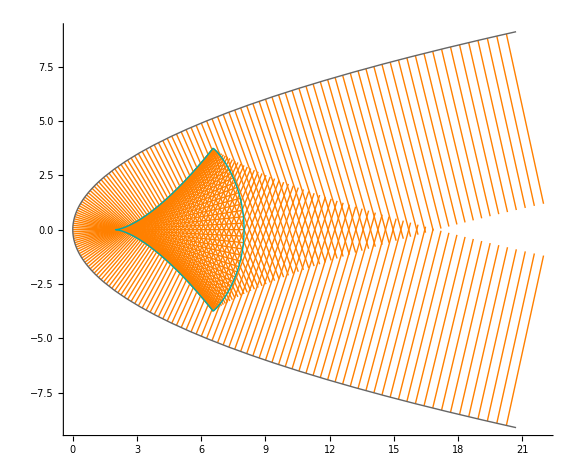

```mathematica
ptLine=Table[{{y^2/4,y},{y^2/4+(2*d)/Sqrt[4+y^2],y-(y*d)/Sqrt[4+y^2]}},{y,-9,9,0.1}];
Show[Graphics[{Orange,Thin,Line[#]}&/@ptLine,Axes->True,AspectRatio->Automatic],
ParametricPlot[{t^2/4,t},{t,-9.1,9.1},PlotStyle->{Thick,GrayLevel[0.4]}],
ParametricPlot[{1/4*(8+3*t^2),-t^3/4},{t,tmin,-tmin},PlotStyle->{Thick,Darker[Cyan]}],
ParametricPlot[{t^2/4+2*d/Sqrt[4+t^2],t-(t*d)/Sqrt[4+t^2]},{t,tmin,-tmin},PlotStyle->{Thick,Darker[Cyan]}],
ImageSize->Large]
```